# Lab 9: Pendulum Motion

The Pendulum Equations

-Graphics-

The motion of a physical pendulum of mass m rotating about an axis through a point P (as shown in above figure) is described by the nonlinear equation

-Graphics-

where 
h = distance of the center of mass of the pendulum from the point P
g = acceleration due to gravity
I = moment of inertia of the pendulum about the rotation axis through the point P
θ = angle made by the pendulum at any instant with the vertical

For small angle oscillations,

so that the non-linear equation becomes linear:

where ω = √(mgh/I) is the angular frequency of motion.

Treating each of the two cylinders along with their screws as point masses, find the moment of inertia I of the physical pendulum, the distance h and then calculate the angular frequency ω using the above relationship. [Hint #1: Your solutions to prelab 9 may be helpful. Hint #2: The center of mass of a system of three point masses in one dimension is x_CM=(m_1 x_1+m_2 x_2+m_3 x_3)/(m_1+m_2+m_3)].

PendSoln and LinearPendSoln are functions capable of solving the non-linear and linear solutions obtained by Mathematica's built in numerical integration function given initial conditions for θ and dθ/dt at time t=0. They have been generalized to take in the initial values as well as the characteristic "frequency" ω. Shift-Enter to define these functions.

```mathematica
PendSoln[θ0sol_,θp0sol_,ωsol_]:=NDSolve[{θ''[t]==-ωsol^2 Sin[θ[t]],
θ'[0]==θp0sol,
θ[0]==θ0sol},{θ,θ'},{t,-(t0max=20),100}];
LinearPendSoln[θ0sol_,θp0sol_,ωsol_]:=NDSolve[{θ''[t]==-ωsol^2 θ[t],
θ'[0]==θp0sol,
θ[0]==θ0sol},{θ,θ'},{t,-t0max,100}];
```

Adjust the sliders below to vary the initial conditions and ω. θp0 here represents the angular velocity at time t=0, i.e. dθ/dt|_(t=0). Note that θ_0 ranges from -179 degrees to 179 degrees.

```mathematica
Manipulate[Plot[{Evaluate[{θ[t]}/.PendSoln[θ0,θp0,ω]],Evaluate[{θ[t]}/.LinearPendSoln[θ0,θp0,ω]]},{t,0,60},PlotLegends->{"Nonlinear","Linear"},Frame->True,FrameLabel->{"t (s)","θ (rad)"}],
{ω,.1,2,.1,Appearance->"Open"},{{θ0,1*(π/180.),"θ_0"},-179*(π/180),179*(π/180),1*(π/180.),Appearance->"Open"},{{θp0,0,"dθ/dt|_(t = 0)"},0,4,.01,Appearance->"Open"}]
```

What is the value of angle θ above which you start to notice a significant difference in the period of the θ vs t graphs for linear and non-linear solutions? In other words, what is the value of the angle θ above which the small angle approximation does not work? Express your answer in degrees.

# Experiment

## Getting started

Download the .nb and .cap file and turn on your Pasco 850 Universal Interface. Open the .cap file with Pasco Capstone software.

Connect the Rotary Motion Sensor by clicking on  on the left-hand toolbar.  Click on the ports indicated in the figure. Select “Rotary Motion Sensor”. Minimize “Hardware Setup”.

You should now be able to collect time-dependence of the angle and the instantaneous angular velocity of the pendulum for different initial conditions. Each time you collect a run, make sure the pendulum is hanging at rest in its equilibrium position before clicking the -Graphics- button. While recording, displace the pendulum by differing amounts and let go from rest, collecting at least 10 oscillations, but not more than 20 to keep the data files sizes manageable.

## Collecting data

Collect a set of data of angle versus time for 10-20 oscillations for a small initial angular displacement. Note the run number and complete the analysis below.

After you have completed the analysis below for small angle, collect a set of data of angle versus time for 10-20 oscillations for a LARGE initial angular displacement. Note the run number and repeat the analysis below for this larger displacement.

## Exporting the data for analysis in Mathematica

One you have collected the data, export to the desktop by clicking on File>>Export and saving to the Desktop as a “.txt” file. Ask your TA if you need help.

# Importing the data

Import the data for small angle oscillations from PASCO Capstone software as a file with extension .txt (you may name it pendulum_motion_small_angle.txt) and save it on Desktop.

Check the name of the directory to ensure it matches where you have stored your data. Shift-Enter the following code for the data file named “test1.txt”. Ask your TA if you need help.

```mathematica
SetDirectory["C:\\Users\\Physics Lab User\\Desktop\\Lab_9"]
```

C:\Users\Physics Lab User\Desktop\Lab_9

```mathematica
thetaS=Import["thetaS.txt","Table"][[3;;,{4,5}]];
```

```mathematica
thetaM=Import["thetaM.txt","Table"][[3;;,{4,5}]];
```

```mathematica
thetaL=Import["thetaL.txt","Table"][[3;;,{4,5}]];
```

```mathematica
timevsangle=Table[{datin[[i,4]],datin[[i,5]]},{i,1,Length[datin]}];
```

```mathematica
t0max= tFdata
```

22.384

```mathematica
tFdata = Max[thetaS[[;;,1]]];
```

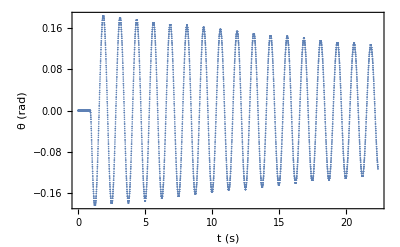

```mathematica
ListPlot[thetaS,PlotRange->All,Frame->True,FrameLabel->{"t (s)","θ (rad)"}]
```

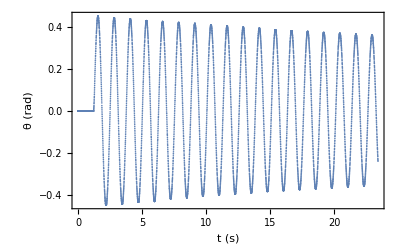

```mathematica
ListPlot[thetaM,PlotRange->All,Frame->True,FrameLabel->{"t (s)","θ (rad)"}]
```

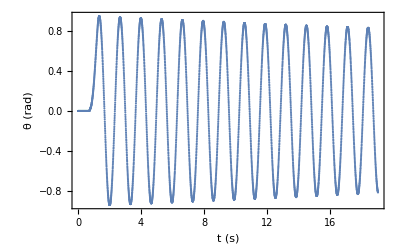

```mathematica
ListPlot[thetaL,PlotRange->All,Frame->True,FrameLabel->{"t (s)","θ (rad)"}]
```

# Plotting the data

Check the plots of the raw data. The plot should match what is seen in PASCO Capstone software. If plots do not seem reasonable, ask the TA.

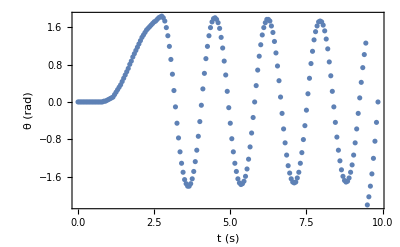

```mathematica
ListPlot[timevsangle,PlotRange->All,Frame->True,FrameLabel->{"t (s)","θ (rad)"}]
```

If everything works correctly, you should see a θ vs t graph where the amplitude of motion decreases with time. Discuss with your group members and explain below why the amplitude decreases with time.

# Fitting and analysis

Shift-Enter the following code.

```mathematica
PendSolnf[θ0sol_,θp0sol_,ωsol_]:=NDSolve[{θ''[t]==-ωsol^2 Sin[θ[t]],
θ'[0]==θp0sol,
θ[0]==θ0sol},{θ,θ'},{t,-t0max,2tFdata}];
LinearPendSolnf[θ0sol_,θp0sol_,ωsol_]:=NDSolve[{θ''[t]==-ωsol^2 θ[t],
θ'[0]==θp0sol,
θ[0]==θ0sol},{θ,θ'},{t,-t0max,2tFdata}];
```

There are a total of 3 coefficients to vary. I suggest you start with ω and then proceed to θ_0 and so forth. It is important that your pendulum start from rest in order to achieve an accurate fit. It is possible you may need to adjust the range of the fit parameters. For example {ω,0,.5,.005,Appearance→"Open"} means ω will have a range [0,0.5] with step size 0.005. Adjust as necessary. Red plot is measured data, blue plot is nonlinear fit and the dotted plot is linear fit. [Notice the difference when you tick mark “ShowHarmonic” and “ShowGridLines”.]

```mathematica
Manipulate[
Show[
ListPlot[thetaM,PlotStyle->Red,PlotRange->{{0,15},{-π,π}}],Plot[Evaluate[{θ[t-t0]}/.PendSolnf[θ0,0,ω]],{t,0,tFdata},PlotStyle->Blue],
Plot[Evaluate[{θ[t-t0]}/.LinearPendSolnf[θ0,0,ω]],{t,0,tFdata},PlotStyle->{Black,Dotted,If[ShowHarmonic,Thickness[0.004],Thickness[0.001]]}],
Frame->True,FrameLabel->{"t (s)","θ (rad)"},GridLines->If[ShowGridLines,{{t0},{θ0,-θ0}},{{None},{None}}]],
{{ω,5.443,"ω"},.01,8.0,.001,Appearance->"Open"},
{{θ0,90*(π/180),"θ_0"},-120*(π/180)0,180*(π/180),.01,Appearance->"Open"},
{t0,0,t0max,.04,Appearance->"Open"},
(*{λ,0,.1,.0001,Appearance->"Open"},*){ShowHarmonic,{False,True}},
{ShowGridLines,{False,True}}]
```

After you have fit your data, copy-paste your plot  and write the fit value to ω below. How close is the fit value to ω from the value you obtained before using the equation ω = √(mgh/I) ? Should the two values of ω be equal in a real-life scenario like yours where the amplitude of motion decreases with time? If yes, why? If not, why not?

Re-execute the Import Data, Plot Data, and Fitting Our Data sections for the large angle oscillations (i.e., for the data file named “pendulum_motion_large_angle.csv”). Copy-paste your plot  and write the fit value to ω below.

How close is the fit value to ω for large oscillations as compared to that for small oscillations? Should they be equal? If yes, why? If not, why not?

Summarize the lab below. Highlight essential findings and comparison of experimental results to theoretical models (linear and non-linear). What did you learn?